# Infection by SARS-CoV-2 with alternate frequencies of mRNA vaccine boosting for patients undergoing antineoplastic treatment for cancer

Jeffrey P. Townsend, Hayley B. Hassler, Brinda Emu, Alex Dornburg

## SARS-CoV-2 (Gudbjartsson)

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-2 S1 IgG antibodies from Gudbjartsson et al. 2020, “Humoral Immune Response to SARS-CoV-2 in Iceland”, New England Journal of Medicine. scaled to post-BNT162b2 (Pfizer-BioNTech) booster vaccination level using the average peak value from 110 naive individuals from Kontopoulou et al. 2022 “Significant Increase in Antibody Titers after the 3rd Booster Dose of the Pfizer–BioNTech mRNA COVID-19 Vaccine in Healthcare Workers in Greece”, Vaccines.

days : 34, 48, 70, 94, 109
OD : 1.6, 1.55, 1.43, 1.19, 1.22

```mathematica
sarscov2data={
{1,34, SARSCoV2,1.6/1.6,  TRUE,NA, NA},
{2,48, SARSCoV2,1.55/1.6, FALSE, (48-34), (1.55/1.6-1.6/1.6)/(48-34)},
{3, 70, SARSCoV2,1.43/1.6,  FALSE,(70-48), (1.43/1.6-1.55/1.6)/(70-48)},
{4, 94, SARSCoV2,1.19/1.6, FALSE,(94-70),  (1.19/1.6-1.43/1.6)/(94-70)}
}
```

{{1,34,SARSCoV2,1.,TRUE,NA,NA},{2,48,SARSCoV2,0.96875,FALSE,14,-0.00223214},{3,70,SARSCoV2,0.89375,FALSE,22,-0.00340909},{4,94,SARSCoV2,0.74375,FALSE,24,-0.00625}}

### SARS-CoV-2 Waning of Antibody OD

```mathematica
sarscov2datalength=Length[sarscov2data]
```

4

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod,  0.75,1, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
sarscov2paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0.75,1.25, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.05,{}},{1.1,{}},{1.15,{}},{1.2,{}},{1.25,{}}}

Mean waning extended to HSCT BNT162b2-scaled peak (1.407611815) from Peeters et al. 2021.

```mathematica
sarscov2meanwaningTLM={{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.0034090909090909124}},{0.95,{-0.0034090909090909124}},{1.,{-0.002232142857142857}}}
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
TableForm[sarscov2meanwaningTLM]
```

0.75 | -0.00625
0.8 | -0.00625
0.85 | -0.00625
0.9 | -0.00340909
0.95 | -0.00340909
1. | -0.00223214

```mathematica
sarscov2antibodywaningTLM=Interpolation[sarscov2meanwaningTLM]
```

InterpolatingFunction[…]

```mathematica
sarscov2antibodytimecourseTLM={1};
day=1;
While[sarscov2antibodytimecourseTLM[[day]]≥0.75,
sarscov2antibodytimecourseTLM=Append[sarscov2antibodytimecourseTLM, sarscov2antibodytimecourseTLM[[day]]+sarscov2antibodywaningTLM[sarscov2antibodytimecourseTLM[[day]]]];
sarscov2antibodytimecourseTLM=Flatten[sarscov2antibodytimecourseTLM];
Increment[day];
];
sarscov2antibodytimecourseTLM
```

{1,0.997768,0.995402,0.992906,0.990284,0.987541,0.984687,0.981728,0.978675,0.97554,0.972332,0.969064,0.965746,0.962391,0.959008,0.955607,0.952197,0.948786,0.945379,0.941982,0.938598,0.935231,0.931879,0.928545,0.925226,0.921921,0.918624,0.915332,0.912039,0.908738,0.90542,0.902076,0.898696,0.895224,0.891577,0.887733,0.883672,0.879371,0.87481,0.869969,0.864831,0.859383,0.853621,0.84755,0.841257,0.834882,0.828462,0.82203,0.815612,0.809229,0.802894,0.796617,0.790399,0.784236,0.778121,0.772038,0.76597,0.759893,0.753779,0.747592}

```mathematica
sarscov2baseline=0.1641335
```

0.164134

This baseline peak-normalized S IgG antibody level for SARS-CoV-2 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
scalarsabove1=Table[(1.422592491177772-0.422592491177772*(index-1)/(Length[sarscov2antibodytimecourseTLM]-1))/1.422592491177772, {index, Length[sarscov2antibodytimecourseTLM]}]
```

{1.,0.994965,0.98993,0.984895,0.97986,0.974826,0.969791,0.964756,0.959721,0.954686,0.949651,0.944616,0.939581,0.934547,0.929512,0.924477,0.919442,0.914407,0.909372,0.904337,0.899302,0.894267,0.889233,0.884198,0.879163,0.874128,0.869093,0.864058,0.859023,0.853988,0.848954,0.843919,0.838884,0.833849,0.828814,0.823779,0.818744,0.813709,0.808675,0.80364,0.798605,0.79357,0.788535,0.7835,0.778465,0.77343,0.768395,0.763361,0.758326,0.753291,0.748256,0.743221,0.738186,0.733151,0.728116,0.723082,0.718047,0.713012,0.707977,0.702942}

```mathematica
sarscov2antibodytimecourseBPtoExp=(sarscov2antibodytimecourseTLM+0.407611815)*scalarsabove1
```

{1.40761,1.3983,1.38889,1.37936,1.36974,1.36003,1.35024,1.34037,1.33045,1.32048,1.31047,1.30043,1.29038,1.28033,1.27029,1.26026,1.25027,1.2403,1.23037,1.22049,1.21065,1.20086,1.19112,1.18143,1.17178,1.16218,1.15262,1.1431,1.13361,1.12415,1.1147,1.10527,1.09584,1.08637,1.07679,1.06708,1.05723,1.04723,1.03706,1.02671,1.01618,1.00545,0.994526,0.983419,0.972201,0.960982,0.949794,0.93866,0.927602,0.916635,0.905768,0.895008,0.884355,0.873805,0.863351,0.852983,0.842687,0.832445,0.822238,0.812042}

```mathematica
Export["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv", sarscov2antibodytimecourseTLM]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

OpenWrite::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv.

$Failed

Used natural infection lambda value imputed in Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2halflife=Log[2]/ lambda /.lambda->0.0044587480795691795
```

155.458

```mathematica
Length[sarscov2antibodytimecourseBPtoExp]
```

60

```mathematica
sarscov2antibodytimecourseB=sarscov2antibodytimecourseBPtoExp;
day=Length[sarscov2antibodytimecourseB];
While[day<4393,
Increment[day];
AppendTo[sarscov2antibodytimecourseB, sarscov2baseline+(sarscov2antibodytimecourseB[[day-1]]- sarscov2baseline)*Exp[-lambda /.lambda->0.0044587480795691795]]
]
```

```mathematica
sarscov2antibodytimecourseB
```

{1.40761,1.3983,1.38889,1.37936,1.36974,1.36003,1.35024,1.34037,1.33045,1.32048,1.31047,1.30043,1.29038,1.28033,1.27029,1.26026,1.25027,1.2403,1.23037,1.22049,1.21065,1.20086,1.19112,1.18143,1.17178,1.16218,1.15262,1.1431,1.13361,1.12415,1.1147,1.10527,1.09584,1.08637,1.07679,1.06708,1.05723,1.04723,1.03706,1.02671,1.01618,1.00545,0.994526,0.983419,0.972201,0.960982,0.949794,0.93866,0.927602,0.916635,0.905768,0.895008,0.884355,0.873805,0.863351,0.852983,0.842687,0.832445,0.822238,0.812042,0.809159,0.80629,0.803433,0.800589,0.797757,0.794938,0.792132,0.789338,0.786557,0.783788,0.781031,0.778286,0.775554,0.772834,0.770126,0.76743,0.764746,0.762074,0.759414,0.756766,0.754129,0.751504,0.748891,0.74629,0.7437,0.741121,0.738555,0.735999,0.733455,0.730922,0.728401,0.72589,0.723391,0.720903,0.718426,0.71596,0.713505,0.711061,0.708628,0.706206,0.703794,0.701393,0.699003,0.696623,0.694254,0.691896,0.689548,0.687211,0.684884,0.682567,0.68026,0.677964,0.675678,0.673403,0.671137,0.668881,0.666636,0.6644,0.662175,0.659959,0.657753,0.655557,0.653371,0.651194,0.649027,0.64687,0.644723,0.642585,0.640456,0.638337,0.636227,0.634127,0.632036,0.629955,0.627882,0.625819,0.623765,0.62172,0.619685,0.617658,0.61564,0.613632,0.611632,0.609641,0.607659,0.605686,0.603721,0.601766,0.599819,0.597881,0.595951,0.59403,0.592117,0.590213,0.588318,0.586431,0.584552,0.582681,0.580819,0.578966,0.57712,0.575283,0.573454,0.571633,0.56982,0.568015,0.566218,0.564429,0.562649,0.560876,0.559111,0.557353,0.555604,0.553862,0.552129,0.550403,0.548684,0.546973,0.54527,0.543574,0.541886,0.540206,0.538533,0.536867,0.535209,0.533558,0.531915,0.530278,0.528649,0.527028,0.525413,0.523806,0.522206,0.520613,0.519027,0.517448,0.515876,0.514311,0.512754,0.511203,0.509659,0.508121,0.506591,0.505068,0.503551,0.502041,0.500538,0.499041,0.497551,0.496068,0.494591,0.493121,0.491657,0.4902,0.488749,0.487305,0.485868,0.484436,0.483011,0.481593,0.48018,0.478774,0.477375,0.475981,0.474594,0.473212,0.471837,0.470468,0.469106,0.467749,0.466398,0.465053,0.463715,0.462382,0.461055,0.459734,0.458419,0.45711,0.455806,0.454509,0.453217,0.451931,0.450651,0.449376,0.448107,0.446844,0.445586,0.444334,0.443087,0.441846,0.440611,0.439381,0.438156,0.436937,0.435723,0.434515,0.433312,0.432115,0.430922,0.429736,0.428554,0.427378,0.426206,0.425041,0.42388,0.422724,0.421574,0.420429,0.419288,0.418153,0.417023,0.415898,0.414778,0.413663,0.412553,0.411448,0.410347,0.409252,0.408162,0.407076,0.405995,0.404919,0.403848,0.402781,0.40172,0.400663,0.39961,0.398563,0.39752,0.396482,0.395448,0.394419,0.393394,0.392374,0.391359,0.390348,0.389342,0.38834,0.387342,0.386349,0.385361,0.384377,0.383397,0.382421,0.38145,0.380483,0.379521,0.378563,0.377609,0.376659,0.375713,0.374772,0.373835,0.372902,0.371973,0.371049,0.370128,0.369212,0.368299,0.367391,0.366487,0.365587,0.36469,0.363798,0.36291,0.362026,0.361145,0.360269,0.359396,0.358527,0.357663,0.356802,0.355945,0.355091,0.354242,0.353396,0.352554,0.351716,0.350881,0.35005,0.349223,0.3484,0.34758,0.346764,0.345951,0.345143,0.344337,0.343536,0.342737,0.341943,0.341152,0.340364,0.33958,0.3388,0.338023,0.337249,0.336479,0.335712,0.334949,0.334189,0.333432,0.332679,0.331929,0.331183,0.33044,0.3297,0.328963,0.32823,0.3275,0.326773,0.32605,0.325329,0.324612,0.323898,0.323187,0.32248,0.321775,0.321074,0.320376,0.319681,0.318989,0.3183,0.317614,0.316931,0.316251,0.315575,0.314901,0.31423,0.313562,0.312898,0.312236,0.311577,0.310921,0.310268,0.309618,0.308971,0.308326,0.307685,0.307046,0.30641,0.305777,0.305147,0.30452,0.303895,0.303274,0.302655,0.302038,0.301425,0.300814,0.300206,0.299601,0.298998,0.298398,0.297801,0.297206,0.296614,0.296024,0.295438,0.294854,0.294272,0.293693,0.293117,0.292543,0.291972,0.291403,0.290837,0.290273,0.289712,0.289153,0.288597,0.288043,0.287492,0.286943,0.286397,0.285853,0.285311,0.284772,0.284236,0.283701,0.283169,0.28264,0.282113,0.281588,0.281065,0.280545,0.280027,0.279511,0.278998,0.278487,0.277978,0.277472,0.276968,0.276466,0.275966,0.275468,0.274973,0.27448,0.273989,0.2735,0.273014,0.272529,0.272047,0.271567,0.271089,0.270613,0.27014,0.269668,0.269199,0.268731,0.268266,0.267803,0.267341,0.266882,0.266425,0.26597,0.265517,0.265066,0.264617,0.26417,0.263725,0.263282,0.262841,0.262401,0.261964,0.261529,0.261096,0.260664,0.260235,0.259807,0.259382,0.258958,0.258536,0.258116,0.257698,0.257282,0.256867,0.256455,0.256044,0.255635,0.255228,0.254823,0.254419,0.254018,0.253618,0.25322,0.252824,0.252429,0.252036,0.251645,0.251256,0.250868,0.250482,0.250098,0.249716,0.249335,0.248956,0.248579,0.248203,0.247829,0.247457,0.247086,0.246717,0.246349,0.245984,0.245619,0.245257,0.244896,0.244537,0.244179,0.243823,0.243468,0.243115,0.242764,0.242414,0.242066,0.241719,0.241374,0.241031,0.240688,0.240348,0.240009,0.239671,0.239335,0.239001,0.238668,0.238336,0.238006,0.237677,0.23735,0.237024,0.2367,0.236377,0.236056,0.235736,0.235417,0.2351,0.234784,0.23447,0.234157,0.233846,0.233536,0.233227,0.232919,0.232613,0.232309,0.232005,0.231703,0.231403,0.231104,0.230806,0.230509,0.230214,0.22992,0.229627,0.229336,0.229046,0.228757,0.228469,0.228183,0.227898,0.227615,0.227332,0.227051,0.226771,0.226492,0.226215,0.225939,0.225664,0.22539,0.225118,0.224846,0.224576,0.224307,0.22404,0.223773,0.223508,0.223244,0.222981,0.222719,0.222458,0.222199,0.22194,0.221683,0.221427,0.221172,0.220919,0.220666,0.220414,0.220164,0.219915,0.219667,0.21942,0.219174,0.218929,0.218685,0.218442,0.218201,0.21796,0.217721,0.217482,0.217245,0.217009,0.216773,0.216539,0.216306,0.216074,0.215843,0.215613,0.215384,0.215156,0.214929,0.214703,0.214478,0.214254,0.214031,0.213809,0.213588,0.213368,0.213149,0.212931,0.212714,0.212498,0.212282,0.212068,0.211855,0.211643,0.211431,0.211221,0.211011,0.210803,0.210595,0.210389,0.210183,0.209978,0.209774,0.209571,0.209369,0.209167,0.208967,0.208768,0.208569,0.208371,0.208175,0.207979,0.207784,0.207589,0.207396,0.207204,0.207012,0.206821,0.206631,0.206442,0.206254,0.206067,0.20588,0.205694,0.20551,0.205325,0.205142,0.20496,0.204778,0.204597,0.204417,0.204238,0.20406,0.203882,0.203705,0.203529,0.203354,0.203179,0.203006,0.202833,0.202661,0.202489,0.202319,0.202149,0.20198,0.201811,0.201644,0.201477,0.201311,0.201145,0.20098,0.200817,0.200653,0.200491,0.200329,0.200168,0.200008,0.199848,0.199689,0.199531,0.199374,0.199217,0.199061,0.198905,0.198751,0.198597,0.198443,0.198291,0.198139,0.197988,0.197837,0.197687,0.197538,0.197389,0.197241,0.197094,0.196947,0.196801,0.196656,0.196511,0.196367,0.196224,0.196081,0.195939,0.195797,0.195657,0.195516,0.195377,0.195238,0.195099,0.194962,0.194824,0.194688,0.194552,0.194417,0.194282,0.194148,0.194014,0.193881,0.193749,0.193617,0.193486,0.193355,0.193225,0.193096,0.192967,0.192839,0.192711,0.192584,0.192457,0.192331,0.192206,0.192081,0.191957,0.191833,0.19171,0.191587,0.191465,0.191343,0.191222,0.191102,0.190982,0.190862,0.190743,0.190625,0.190507,0.19039,0.190273,0.190157,0.190041,0.189926,0.189811,0.189697,0.189583,0.18947,0.189357,0.189245,0.189133,0.189022,0.188911,0.188801,0.188691,0.188582,0.188473,0.188365,0.188257,0.18815,0.188043,0.187937,0.187831,0.187725,0.18762,0.187516,0.187412,0.187308,0.187205,0.187103,0.187,0.186899,0.186797,0.186697,0.186596,0.186496,0.186397,0.186298,0.186199,0.186101,0.186003,0.185906,0.185809,0.185713,0.185617,0.185521,0.185426,0.185331,0.185237,0.185143,0.185049,0.184956,0.184864,0.184772,0.18468,0.184588,0.184497,0.184407,0.184317,0.184227,0.184137,0.184048,0.18396,0.183872,0.183784,0.183696,0.183609,0.183523,0.183436,0.183351,0.183265,0.18318,0.183095,0.183011,0.182927,0.182843,0.18276,0.182677,0.182595,0.182513,0.182431,0.182349,0.182268,0.182188,0.182107,0.182027,0.181948,0.181868,0.18179,0.181711,0.181633,0.181555,0.181477,0.1814,0.181324,0.181247,0.181171,0.181095,0.18102,0.180945,0.18087,0.180795,0.180721,0.180647,0.180574,0.180501,0.180428,0.180355,0.180283,0.180211,0.18014,0.180069,0.179998,0.179927,0.179857,0.179787,0.179717,0.179648,0.179579,0.17951,0.179442,0.179374,0.179306,0.179238,0.179171,0.179104,0.179038,0.178971,0.178905,0.17884,0.178774,0.178709,0.178644,0.17858,0.178516,0.178452,0.178388,0.178324,0.178261,0.178198,0.178136,0.178074,0.178012,0.17795,0.177888,0.177827,0.177766,0.177706,0.177645,0.177585,0.177525,0.177466,0.177406,0.177347,0.177289,0.17723,0.177172,0.177114,0.177056,0.176998,0.176941,0.176884,0.176828,0.176771,0.176715,0.176659,0.176603,0.176548,0.176492,0.176437,0.176383,0.176328,0.176274,0.17622,0.176166,0.176113,0.176059,0.176006,0.175954,0.175901,0.175849,0.175796,0.175745,0.175693,0.175641,0.17559,0.175539,0.175489,0.175438,0.175388,0.175338,0.175288,0.175238,0.175189,0.17514,0.175091,0.175042,0.174993,0.174945,0.174897,0.174849,0.174801,0.174754,0.174707,0.17466,0.174613,0.174566,0.17452,0.174474,0.174428,0.174382,0.174336,0.174291,0.174246,0.174201,0.174156,0.174111,0.174067,0.174023,0.173979,0.173935,0.173891,0.173848,0.173805,0.173762,0.173719,0.173676,0.173634,0.173591,0.173549,0.173507,0.173466,0.173424,0.173383,0.173342,0.173301,0.17326,0.173219,0.173179,0.173139,0.173099,0.173059,0.173019,0.17298,0.17294,0.172901,0.172862,0.172823,0.172785,0.172746,0.172708,0.17267,0.172632,0.172594,0.172556,0.172519,0.172481,0.172444,0.172407,0.17237,0.172334,0.172297,0.172261,0.172225,0.172189,0.172153,0.172117,0.172082,0.172046,0.172011,0.171976,0.171941,0.171907,0.171872,0.171838,0.171803,0.171769,0.171735,0.171701,0.171668,0.171634,0.171601,0.171568,0.171535,0.171502,0.171469,0.171436,0.171404,0.171371,0.171339,0.171307,0.171275,0.171243,0.171212,0.17118,0.171149,0.171118,0.171087,0.171056,0.171025,0.170994,0.170964,0.170933,0.170903,0.170873,0.170843,0.170813,0.170783,0.170754,0.170724,0.170695,0.170666,0.170637,0.170608,0.170579,0.17055,0.170522,0.170493,0.170465,0.170437,0.170409,0.170381,0.170353,0.170326,0.170298,0.170271,0.170243,0.170216,0.170189,0.170162,0.170135,0.170109,0.170082,0.170056,0.170029,0.170003,0.169977,0.169951,0.169925,0.169899,0.169874,0.169848,0.169823,0.169797,0.169772,0.169747,0.169722,0.169697,0.169672,0.169648,0.169623,0.169599,0.169575,0.16955,0.169526,0.169502,0.169478,0.169455,0.169431,0.169407,0.169384,0.169361,0.169337,0.169314,0.169291,0.169268,0.169245,0.169223,0.1692,0.169177,0.169155,0.169133,0.16911,0.169088,0.169066,0.169044,0.169022,0.169001,0.168979,0.168957,0.168936,0.168915,0.168893,0.168872,0.168851,0.16883,0.168809,0.168788,0.168768,0.168747,0.168727,0.168706,0.168686,0.168665,0.168645,0.168625,0.168605,0.168585,0.168566,0.168546,0.168526,0.168507,0.168487,0.168468,0.168449,0.168429,0.16841,0.168391,0.168372,0.168353,0.168335,0.168316,0.168297,0.168279,0.16826,0.168242,0.168224,0.168206,0.168187,0.168169,0.168151,0.168134,0.168116,0.168098,0.16808,0.168063,0.168045,0.168028,0.168011,0.167993,0.167976,0.167959,0.167942,0.167925,0.167908,0.167892,0.167875,0.167858,0.167842,0.167825,0.167809,0.167792,0.167776,0.16776,0.167744,0.167728,0.167712,0.167696,0.16768,0.167664,0.167648,0.167633,0.167617,0.167602,0.167586,0.167571,0.167556,0.16754,0.167525,0.16751,0.167495,0.16748,0.167465,0.16745,0.167436,0.167421,0.167406,0.167392,0.167377,0.167363,0.167349,0.167334,0.16732,0.167306,0.167292,0.167278,0.167264,0.16725,0.167236,0.167222,0.167208,0.167195,0.167181,0.167167,0.167154,0.167141,0.167127,0.167114,0.167101,0.167087,0.167074,0.167061,0.167048,0.167035,0.167022,0.167009,0.166997,0.166984,0.166971,0.166959,0.166946,0.166933,0.166921,0.166909,0.166896,0.166884,0.166872,0.16686,0.166847,0.166835,0.166823,0.166811,0.166799,0.166788,0.166776,0.166764,0.166752,0.166741,0.166729,0.166718,0.166706,0.166695,0.166683,0.166672,0.166661,0.166649,0.166638,0.166627,0.166616,0.166605,0.166594,0.166583,0.166572,0.166561,0.16655,0.16654,0.166529,0.166518,0.166508,0.166497,0.166487,0.166476,0.166466,0.166455,0.166445,0.166435,0.166424,0.166414,0.166404,0.166394,0.166384,0.166374,0.166364,0.166354,0.166344,0.166334,0.166325,0.166315,0.166305,0.166295,0.166286,0.166276,0.166267,0.166257,0.166248,0.166238,0.166229,0.16622,0.16621,0.166201,0.166192,0.166183,0.166174,0.166165,0.166156,0.166147,0.166138,0.166129,0.16612,0.166111,0.166102,0.166093,0.166085,0.166076,0.166067,0.166059,0.16605,0.166042,0.166033,0.166025,0.166016,0.166008,0.166,0.165991,0.165983,0.165975,0.165967,0.165958,0.16595,0.165942,0.165934,0.165926,0.165918,0.16591,0.165902,0.165895,0.165887,0.165879,0.165871,0.165863,0.165856,0.165848,0.16584,0.165833,0.165825,0.165818,0.16581,0.165803,0.165795,0.165788,0.165781,0.165773,0.165766,0.165759,0.165752,0.165744,0.165737,0.16573,0.165723,0.165716,0.165709,0.165702,0.165695,0.165688,0.165681,0.165674,0.165667,0.16566,0.165654,0.165647,0.16564,0.165633,0.165627,0.16562,0.165613,0.165607,0.1656,0.165594,0.165587,0.165581,0.165574,0.165568,0.165562,0.165555,0.165549,0.165543,0.165536,0.16553,0.165524,0.165518,0.165512,0.165505,0.165499,0.165493,0.165487,0.165481,0.165475,0.165469,0.165463,0.165457,0.165451,0.165446,0.16544,0.165434,0.165428,0.165422,0.165417,0.165411,0.165405,0.1654,0.165394,0.165388,0.165383,0.165377,0.165372,0.165366,0.165361,0.165355,0.16535,0.165344,0.165339,0.165334,0.165328,0.165323,0.165318,0.165312,0.165307,0.165302,0.165297,0.165292,0.165286,0.165281,0.165276,0.165271,0.165266,0.165261,0.165256,0.165251,0.165246,0.165241,0.165236,0.165231,0.165226,0.165222,0.165217,0.165212,0.165207,0.165202,0.165198,0.165193,0.165188,0.165183,0.165179,0.165174,0.165169,0.165165,0.16516,0.165156,0.165151,0.165147,0.165142,0.165138,0.165133,0.165129,0.165124,0.16512,0.165115,0.165111,0.165107,0.165102,0.165098,0.165094,0.16509,0.165085,0.165081,0.165077,0.165073,0.165068,0.165064,0.16506,0.165056,0.165052,0.165048,0.165044,0.16504,0.165036,0.165032,0.165028,0.165024,0.16502,0.165016,0.165012,0.165008,0.165004,0.165,0.164996,0.164993,0.164989,0.164985,0.164981,0.164977,0.164974,0.16497,0.164966,0.164962,0.164959,0.164955,0.164951,0.164948,0.164944,0.164941,0.164937,0.164933,0.16493,0.164926,0.164923,0.164919,0.164916,0.164912,0.164909,0.164905,0.164902,0.164899,0.164895,0.164892,0.164888,0.164885,0.164882,0.164878,0.164875,0.164872,0.164868,0.164865,0.164862,0.164859,0.164855,0.164852,0.164849,0.164846,0.164843,0.16484,0.164836,0.164833,0.16483,0.164827,0.164824,0.164821,0.164818,0.164815,0.164812,0.164809,0.164806,0.164803,0.1648,0.164797,0.164794,0.164791,0.164788,0.164785,0.164782,0.164779,0.164776,0.164774,0.164771,0.164768,0.164765,0.164762,0.164759,0.164757,0.164754,0.164751,0.164748,0.164746,0.164743,0.16474,0.164737,0.164735,0.164732,0.164729,0.164727,0.164724,0.164722,0.164719,0.164716,0.164714,0.164711,0.164709,0.164706,0.164703,0.164701,0.164698,0.164696,0.164693,0.164691,0.164688,0.164686,0.164684,0.164681,0.164679,0.164676,0.164674,0.164671,0.164669,0.164667,0.164664,0.164662,0.16466,0.164657,0.164655,0.164653,0.16465,0.164648,0.164646,0.164643,0.164641,0.164639,0.164637,0.164634,0.164632,0.16463,0.164628,0.164625,0.164623,0.164621,0.164619,0.164617,0.164615,0.164613,0.16461,0.164608,0.164606,0.164604,0.164602,0.1646,0.164598,0.164596,0.164594,0.164592,0.16459,0.164588,0.164586,0.164584,0.164582,0.16458,0.164578,0.164576,0.164574,0.164572,0.16457,0.164568,0.164566,0.164564,0.164562,0.16456,0.164558,0.164556,0.164554,0.164553,0.164551,0.164549,0.164547,0.164545,0.164543,0.164541,0.16454,0.164538,0.164536,0.164534,0.164532,0.164531,0.164529,0.164527,0.164525,0.164524,0.164522,0.16452,0.164518,0.164517,0.164515,0.164513,0.164512,0.16451,0.164508,0.164507,0.164505,0.164503,0.164502,0.1645,0.164498,0.164497,0.164495,0.164494,0.164492,0.16449,0.164489,0.164487,0.164486,0.164484,0.164483,0.164481,0.164479,0.164478,0.164476,0.164475,0.164473,0.164472,0.16447,0.164469,0.164467,0.164466,0.164464,0.164463,0.164461,0.16446,0.164458,0.164457,0.164456,0.164454,0.164453,0.164451,0.16445,0.164449,0.164447,0.164446,0.164444,0.164443,0.164442,0.16444,0.164439,0.164437,0.164436,0.164435,0.164433,0.164432,0.164431,0.164429,0.164428,0.164427,0.164426,0.164424,0.164423,0.164422,0.16442,0.164419,0.164418,0.164417,0.164415,0.164414,0.164413,0.164412,0.16441,0.164409,0.164408,0.164407,0.164405,0.164404,0.164403,0.164402,0.164401,0.164399,0.164398,0.164397,0.164396,0.164395,0.164394,0.164392,0.164391,0.16439,0.164389,0.164388,0.164387,0.164386,0.164384,0.164383,0.164382,0.164381,0.16438,0.164379,0.164378,0.164377,0.164376,0.164375,0.164373,0.164372,0.164371,0.16437,0.164369,0.164368,0.164367,0.164366,0.164365,0.164364,0.164363,0.164362,0.164361,0.16436,0.164359,0.164358,0.164357,0.164356,0.164355,0.164354,0.164353,0.164352,0.164351,0.16435,0.164349,0.164348,0.164347,0.164346,0.164345,0.164344,0.164343,0.164343,0.164342,0.164341,0.16434,0.164339,0.164338,0.164337,0.164336,0.164335,0.164334,0.164333,0.164333,0.164332,0.164331,0.16433,0.164329,0.164328,0.164327,0.164326,0.164326,0.164325,0.164324,0.164323,0.164322,0.164321,0.16432,0.16432,0.164319,0.164318,0.164317,0.164316,0.164316,0.164315,0.164314,0.164313,0.164312,0.164312,0.164311,0.16431,0.164309,0.164308,0.164308,0.164307,0.164306,0.164305,0.164305,0.164304,0.164303,0.164302,0.164301,0.164301,0.1643,0.164299,0.164299,0.164298,0.164297,0.164296,0.164296,0.164295,0.164294,0.164293,0.164293,0.164292,0.164291,0.164291,0.16429,0.164289,0.164289,0.164288,0.164287,0.164286,0.164286,0.164285,0.164284,0.164284,0.164283,0.164282,0.164282,0.164281,0.16428,0.16428,0.164279,0.164279,0.164278,0.164277,0.164277,0.164276,0.164275,0.164275,0.164274,0.164273,0.164273,0.164272,0.164272,0.164271,0.16427,0.16427,0.164269,0.164269,0.164268,0.164267,0.164267,0.164266,0.164266,0.164265,0.164264,0.164264,0.164263,0.164263,0.164262,0.164261,0.164261,0.16426,0.16426,0.164259,0.164259,0.164258,0.164258,0.164257,0.164256,0.164256,0.164255,0.164255,0.164254,0.164254,0.164253,0.164253,0.164252,0.164252,0.164251,0.164251,0.16425,0.16425,0.164249,0.164248,0.164248,0.164247,0.164247,0.164246,0.164246,0.164245,0.164245,0.164244,0.164244,0.164243,0.164243,0.164243,0.164242,0.164242,0.164241,0.164241,0.16424,0.16424,0.164239,0.164239,0.164238,0.164238,0.164237,0.164237,0.164236,0.164236,0.164235,0.164235,0.164235,0.164234,0.164234,0.164233,0.164233,0.164232,0.164232,0.164231,0.164231,0.164231,0.16423,0.16423,0.164229,0.164229,0.164228,0.164228,0.164228,0.164227,0.164227,0.164226,0.164226,0.164226,0.164225,0.164225,0.164224,0.164224,0.164223,0.164223,0.164223,0.164222,0.164222,0.164222,0.164221,0.164221,0.16422,0.16422,0.16422,0.164219,0.164219,0.164218,0.164218,0.164218,0.164217,0.164217,0.164217,0.164216,0.164216,0.164215,0.164215,0.164215,0.164214,0.164214,0.164214,0.164213,0.164213,0.164213,0.164212,0.164212,0.164212,0.164211,0.164211,0.16421,0.16421,0.16421,0.164209,0.164209,0.164209,0.164208,0.164208,0.164208,0.164207,0.164207,0.164207,0.164206,0.164206,0.164206,0.164206,0.164205,0.164205,0.164205,0.164204,0.164204,0.164204,0.164203,0.164203,0.164203,0.164202,0.164202,0.164202,0.164201,0.164201,0.164201,0.164201,0.1642,0.1642,0.1642,0.164199,0.164199,0.164199,0.164198,0.164198,0.164198,0.164198,0.164197,0.164197,0.164197,0.164196,0.164196,0.164196,0.164196,0.164195,0.164195,0.164195,0.164195,0.164194,0.164194,0.164194,0.164193,0.164193,0.164193,0.164193,0.164192,0.164192,0.164192,0.164192,0.164191,0.164191,0.164191,0.164191,0.16419,0.16419,0.16419,0.16419,0.164189,0.164189,0.164189,0.164189,0.164188,0.164188,0.164188,0.164188,0.164187,0.164187,0.164187,0.164187,0.164186,0.164186,0.164186,0.164186,0.164186,0.164185,0.164185,0.164185,0.164185,0.164184,0.164184,0.164184,0.164184,0.164183,0.164183,0.164183,0.164183,0.164183,0.164182,0.164182,0.164182,0.164182,0.164181,0.164181,0.164181,0.164181,0.164181,0.16418,0.16418,0.16418,0.16418,0.16418,0.164179,0.164179,0.164179,0.164179,0.164179,0.164178,0.164178,0.164178,0.164178,0.164178,0.164177,0.164177,0.164177,0.164177,0.164177,0.164176,0.164176,0.164176,0.164176,0.164176,0.164175,0.164175,0.164175,0.164175,0.164175,0.164175,0.164174,0.164174,0.164174,0.164174,0.164174,0.164173,0.164173,0.164173,0.164173,0.164173,0.164173,0.164172,0.164172,0.164172,0.164172,0.164172,0.164172,0.164171,0.164171,0.164171,0.164171,0.164171,0.164171,0.16417,0.16417,0.16417,0.16417,0.16417,0.16417,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134}

```mathematica
sarscov2antibodytimecourseB[[150]]
```

0.597881

```mathematica
1.675000077*(10^3.02)/(10^3.373)
```

0.743045

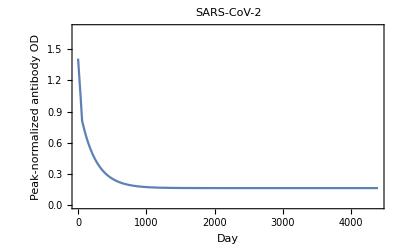

```mathematica
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster04May2023.pdf.

$Failed

### SARS-CoV-2 Probability of Infection | Antibody OD

```mathematica
sarscov2probinfgivenaod[aod_]:=1/(1+Exp[-(-5.841733+-5.323444*aod)])
```

These values for a and b come from the ancestral and descendent states natural infection analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2probinfgivenaod[aod]
```

1/(1+ⅇ^(5.84173+5.32344 aod))

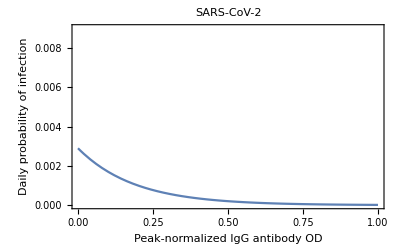

```mathematica
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster04May2023.pdf.

$Failed

```mathematica
sarscov2probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

### SARS-CoV-2 Probability of No Reinfection Time Course

```mathematica
sarscov2probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov2probnoreinfectiontimecourse, 
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov2probnoreinfectiontimecourse, 
If[day<Length[sarscov2antibodytimecourseB],
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]] ]),
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]])
]
]
];

sarscov2probnoreinfectiontimecourse
```

{1,0.999998,0.999997,0.999995,0.999993,0.999991,0.999988,0.999986,0.999984,0.999981,0.999978,0.999975,0.999972,0.999969,0.999966,0.999962,0.999959,0.999955,0.999951,0.999946,0.999942,0.999937,0.999932,0.999926,0.999921,0.999915,0.999908,0.999902,0.999895,0.999887,0.99988,0.999872,0.999863,0.999854,0.999845,0.999835,0.999824,0.999813,0.999802,0.99979,0.999777,0.999763,0.999748,0.999733,0.999716,0.999699,0.99968,0.999661,0.99964,0.999618,0.999595,0.99957,0.999544,0.999516,0.999487,0.999456,0.999423,0.999388,0.999352,0.999314,0.999274,0.999235,0.999194,0.999154,0.999112,0.99907,0.999027,0.998984,0.99894,0.998895,0.99885,0.998804,0.998757,0.998709,0.998661,0.998613,0.998563,0.998513,0.998462,0.998411,0.998358,0.998305,0.998251,0.998197,0.998141,0.998085,0.998029,0.997971,0.997913,0.997853,0.997793,0.997733,0.997671,0.997609,0.997545,0.997481,0.997416,0.997351,0.997284,0.997217,0.997148,0.997079,0.997009,0.996938,0.996866,0.996793,0.99672,0.996645,0.99657,0.996493,0.996416,0.996337,0.996258,0.996178,0.996097,0.996014,0.995931,0.995847,0.995762,0.995676,0.995589,0.9955,0.995411,0.995321,0.99523,0.995137,0.995044,0.99495,0.994854,0.994758,0.99466,0.994561,0.994461,0.99436,0.994258,0.994155,0.994051,0.993945,0.993839,0.993731,0.993622,0.993512,0.993401,0.993289,0.993175,0.99306,0.992945,0.992827,0.992709,0.99259,0.992469,0.992347,0.992224,0.992099,0.991973,0.991847,0.991718,0.991589,0.991458,0.991326,0.991193,0.991058,0.990922,0.990785,0.990647,0.990507,0.990366,0.990223,0.990079,0.989934,0.989788,0.98964,0.989491,0.98934,0.989188,0.989035,0.98888,0.988724,0.988566,0.988407,0.988247,0.988085,0.987922,0.987757,0.987591,0.987424,0.987255,0.987085,0.986913,0.98674,0.986565,0.986389,0.986211,0.986032,0.985851,0.985669,0.985485,0.9853,0.985114,0.984926,0.984736,0.984545,0.984352,0.984158,0.983962,0.983765,0.983566,0.983365,0.983163,0.98296,0.982755,0.982548,0.98234,0.98213,0.981919,0.981706,0.981491,0.981275,0.981057,0.980838,0.980617,0.980394,0.98017,0.979944,0.979717,0.979488,0.979257,0.979025,0.978791,0.978555,0.978318,0.978079,0.977839,0.977597,0.977353,0.977107,0.97686,0.976611,0.976361,0.976109,0.975855,0.975599,0.975342,0.975083,0.974823,0.97456,0.974297,0.974031,0.973764,0.973495,0.973224,0.972951,0.972677,0.972402,0.972124,0.971845,0.971564,0.971281,0.970997,0.970711,0.970423,0.970133,0.969842,0.969549,0.969254,0.968958,0.96866,0.96836,0.968058,0.967755,0.967449,0.967143,0.966834,0.966524,0.966212,0.965898,0.965582,0.965265,0.964946,0.964625,0.964303,0.963978,0.963652,0.963325,0.962995,0.962664,0.962331,0.961996,0.96166,0.961322,0.960982,0.96064,0.960297,0.959951,0.959604,0.959256,0.958905,0.958553,0.958199,0.957843,0.957486,0.957127,0.956766,0.956403,0.956039,0.955673,0.955305,0.954935,0.954564,0.954191,0.953816,0.95344,0.953061,0.952681,0.9523,0.951916,0.951531,0.951144,0.950755,0.950365,0.949973,0.949579,0.949184,0.948786,0.948387,0.947987,0.947584,0.94718,0.946775,0.946367,0.945958,0.945547,0.945134,0.94472,0.944304,0.943886,0.943467,0.943046,0.942623,0.942199,0.941773,0.941345,0.940915,0.940484,0.940051,0.939617,0.939181,0.938743,0.938303,0.937862,0.93742,0.936975,0.936529,0.936081,0.935632,0.935181,0.934728,0.934274,0.933818,0.933361,0.932902,0.932441,0.931979,0.931515,0.931049,0.930582,0.930113,0.929643,0.929171,0.928697,0.928222,0.927745,0.927267,0.926787,0.926306,0.925823,0.925338,0.924852,0.924365,0.923875,0.923385,0.922892,0.922398,0.921903,0.921406,0.920908,0.920408,0.919906,0.919403,0.918899,0.918393,0.917885,0.917377,0.916866,0.916354,0.915841,0.915326,0.914809,0.914292,0.913772,0.913252,0.912729,0.912206,0.911681,0.911154,0.910626,0.910097,0.909566,0.909034,0.9085,0.907965,0.907429,0.906891,0.906352,0.905811,0.905269,0.904726,0.904181,0.903635,0.903087,0.902539,0.901988,0.901437,0.900884,0.90033,0.899774,0.899218,0.898659,0.8981,0.897539,0.896977,0.896414,0.895849,0.895283,0.894716,0.894147,0.893577,0.893006,0.892434,0.89186,0.891286,0.89071,0.890132,0.889554,0.888974,0.888393,0.887811,0.887227,0.886643,0.886057,0.88547,0.884882,0.884292,0.883702,0.88311,0.882517,0.881923,0.881328,0.880732,0.880134,0.879535,0.878936,0.878335,0.877733,0.87713,0.876526,0.87592,0.875314,0.874706,0.874098,0.873488,0.872877,0.872266,0.871653,0.871039,0.870424,0.869808,0.869191,0.868573,0.867954,0.867334,0.866713,0.86609,0.865467,0.864843,0.864218,0.863592,0.862965,0.862337,0.861708,0.861078,0.860447,0.859815,0.859182,0.858549,0.857914,0.857278,0.856642,0.856004,0.855366,0.854727,0.854087,0.853446,0.852804,0.852161,0.851517,0.850873,0.850228,0.849581,0.848934,0.848286,0.847638,0.846988,0.846338,0.845686,0.845034,0.844381,0.843728,0.843073,0.842418,0.841762,0.841105,0.840448,0.83979,0.83913,0.838471,0.83781,0.837149,0.836487,0.835824,0.83516,0.834496,0.833831,0.833165,0.832499,0.831832,0.831164,0.830496,0.829827,0.829157,0.828487,0.827815,0.827144,0.826471,0.825798,0.825124,0.82445,0.823775,0.8231,0.822423,0.821747,0.821069,0.820391,0.819713,0.819033,0.818354,0.817673,0.816992,0.816311,0.815629,0.814946,0.814263,0.813579,0.812895,0.81221,0.811525,0.810839,0.810153,0.809466,0.808778,0.808091,0.807402,0.806713,0.806024,0.805334,0.804644,0.803953,0.803262,0.80257,0.801878,0.801186,0.800493,0.799799,0.799105,0.798411,0.797716,0.797021,0.796325,0.795629,0.794933,0.794236,0.793539,0.792842,0.792144,0.791445,0.790747,0.790048,0.789348,0.788649,0.787949,0.787248,0.786547,0.785846,0.785145,0.784443,0.783741,0.783039,0.782336,0.781633,0.780929,0.780226,0.779522,0.778818,0.778113,0.777409,0.776704,0.775998,0.775293,0.774587,0.773881,0.773175,0.772468,0.771761,0.771054,0.770347,0.76964,0.768932,0.768224,0.767516,0.766808,0.766099,0.76539,0.764681,0.763972,0.763263,0.762554,0.761844,0.761134,0.760424,0.759714,0.759004,0.758293,0.757583,0.756872,0.756161,0.75545,0.754739,0.754028,0.753316,0.752605,0.751893,0.751182,0.75047,0.749758,0.749046,0.748334,0.747622,0.746909,0.746197,0.745484,0.744772,0.744059,0.743347,0.742634,0.741921,0.741208,0.740496,0.739783,0.73907,0.738357,0.737644,0.736931,0.736218,0.735505,0.734792,0.734078,0.733365,0.732652,0.731939,0.731226,0.730513,0.7298,0.729087,0.728374,0.72766,0.726947,0.726234,0.725521,0.724809,0.724096,0.723383,0.72267,0.721957,0.721245,0.720532,0.719819,0.719107,0.718394,0.717682,0.71697,0.716257,0.715545,0.714833,0.714121,0.713409,0.712698,0.711986,0.711274,0.710563,0.709851,0.70914,0.708429,0.707718,0.707007,0.706296,0.705586,0.704875,0.704165,0.703455,0.702744,0.702034,0.701325,0.700615,0.699905,0.699196,0.698487,0.697778,0.697069,0.69636,0.695652,0.694943,0.694235,0.693527,0.692819,0.692112,0.691404,0.690697,0.68999,0.689283,0.688576,0.68787,0.687164,0.686457,0.685752,0.685046,0.684341,0.683635,0.68293,0.682226,0.681521,0.680817,0.680113,0.679409,0.678705,0.678002,0.677299,0.676596,0.675893,0.675191,0.674489,0.673787,0.673085,0.672384,0.671683,0.670982,0.670282,0.669581,0.668881,0.668182,0.667482,0.666783,0.666084,0.665386,0.664687,0.663989,0.663292,0.662594,0.661897,0.6612,0.660504,0.659807,0.659112,0.658416,0.657721,0.657026,0.656331,0.655637,0.654942,0.654249,0.653555,0.652862,0.65217,0.651477,0.650785,0.650093,0.649402,0.648711,0.64802,0.64733,0.64664,0.64595,0.64526,0.644571,0.643883,0.643195,0.642507,0.641819,0.641132,0.640445,0.639758,0.639072,0.638386,0.637701,0.637016,0.636331,0.635647,0.634963,0.634279,0.633596,0.632914,0.632231,0.631549,0.630867,0.630186,0.629505,0.628825,0.628145,0.627465,0.626786,0.626107,0.625429,0.62475,0.624073,0.623396,0.622719,0.622042,0.621366,0.620691,0.620015,0.61934,0.618666,0.617992,0.617319,0.616645,0.615973,0.6153,0.614629,0.613957,0.613286,0.612615,0.611945,0.611276,0.610606,0.609937,0.609269,0.608601,0.607933,0.607266,0.6066,0.605933,0.605268,0.604602,0.603937,0.603273,0.602609,0.601945,0.601282,0.60062,0.599958,0.599296,0.598634,0.597974,0.597313,0.596653,0.595994,0.595335,0.594676,0.594018,0.593361,0.592704,0.592047,0.591391,0.590735,0.59008,0.589425,0.588771,0.588117,0.587464,0.586811,0.586158,0.585507,0.584855,0.584204,0.583554,0.582904,0.582254,0.581605,0.580957,0.580309,0.579661,0.579014,0.578367,0.577721,0.577076,0.57643,0.575786,0.575142,0.574498,0.573855,0.573212,0.57257,0.571929,0.571287,0.570647,0.570007,0.569367,0.568728,0.568089,0.567451,0.566813,0.566176,0.56554,0.564904,0.564268,0.563633,0.562998,0.562364,0.561731,0.561098,0.560465,0.559833,0.559202,0.558571,0.55794,0.55731,0.556681,0.556052,0.555423,0.554795,0.554168,0.553541,0.552915,0.552289,0.551664,0.551039,0.550415,0.549791,0.549168,0.548545,0.547923,0.547301,0.54668,0.54606,0.54544,0.54482,0.544201,0.543583,0.542965,0.542347,0.54173,0.541114,0.540498,0.539883,0.539268,0.538654,0.53804,0.537427,0.536814,0.536202,0.535591,0.53498,0.534369,0.533759,0.53315,0.532541,0.531933,0.531325,0.530718,0.530111,0.529505,0.528899,0.528294,0.52769,0.527086,0.526482,0.525879,0.525277,0.524675,0.524074,0.523473,0.522873,0.522273,0.521674,0.521075,0.520477,0.51988,0.519283,0.518686,0.51809,0.517495,0.5169,0.516306,0.515713,0.515119,0.514527,0.513935,0.513343,0.512752,0.512162,0.511572,0.510983,0.510394,0.509806,0.509218,0.508631,0.508045,0.507459,0.506873,0.506288,0.505704,0.50512,0.504537,0.503954,0.503372,0.50279,0.502209,0.501629,0.501049,0.50047,0.499891,0.499312,0.498735,0.498158,0.497581,0.497005,0.496429,0.495854,0.49528,0.494706,0.494133,0.49356,0.492988,0.492416,0.491845,0.491275,0.490705,0.490135,0.489566,0.488998,0.48843,0.487863,0.487296,0.48673,0.486165,0.4856,0.485035,0.484471,0.483908,0.483345,0.482783,0.482221,0.48166,0.4811,0.48054,0.47998,0.479421,0.478863,0.478305,0.477748,0.477191,0.476635,0.47608,0.475525,0.47497,0.474416,0.473863,0.47331,0.472758,0.472206,0.471655,0.471104,0.470554,0.470005,0.469456,0.468908,0.46836,0.467812,0.467266,0.46672,0.466174,0.465629,0.465084,0.46454,0.463997,0.463454,0.462912,0.46237,0.461829,0.461288,0.460748,0.460209,0.45967,0.459131,0.458594,0.458056,0.457519,0.456983,0.456448,0.455912,0.455378,0.454844,0.45431,0.453778,0.453245,0.452713,0.452182,0.451651,0.451121,0.450592,0.450063,0.449534,0.449006,0.448479,0.447952,0.447426,0.4469,0.446375,0.44585,0.445326,0.444802,0.444279,0.443757,0.443235,0.442713,0.442193,0.441672,0.441153,0.440633,0.440115,0.439597,0.439079,0.438562,0.438046,0.43753,0.437014,0.436499,0.435985,0.435471,0.434958,0.434446,0.433933,0.433422,0.432911,0.4324,0.43189,0.431381,0.430872,0.430364,0.429856,0.429349,0.428842,0.428336,0.42783,0.427325,0.426821,0.426317,0.425813,0.42531,0.424808,0.424306,0.423805,0.423304,0.422804,0.422304,0.421805,0.421306,0.420808,0.420311,0.419814,0.419317,0.418821,0.418326,0.417831,0.417337,0.416843,0.41635,0.415857,0.415365,0.414873,0.414382,0.413892,0.413402,0.412912,0.412423,0.411935,0.411447,0.410959,0.410472,0.409986,0.4095,0.409015,0.40853,0.408046,0.407562,0.407079,0.406596,0.406114,0.405633,0.405152,0.404671,0.404191,0.403712,0.403233,0.402754,0.402276,0.401799,0.401322,0.400846,0.40037,0.399895,0.39942,0.398946,0.398472,0.397999,0.397526,0.397054,0.396582,0.396111,0.395641,0.395171,0.394701,0.394232,0.393764,0.393296,0.392828,0.392361,0.391895,0.391429,0.390963,0.390499,0.390034,0.38957,0.389107,0.388644,0.388182,0.38772,0.387259,0.386798,0.386338,0.385878,0.385419,0.38496,0.384502,0.384044,0.383587,0.38313,0.382674,0.382218,0.381763,0.381309,0.380855,0.380401,0.379948,0.379495,0.379043,0.378591,0.37814,0.37769,0.37724,0.37679,0.376341,0.375893,0.375444,0.374997,0.37455,0.374103,0.373657,0.373212,0.372767,0.372322,0.371878,0.371435,0.370991,0.370549,0.370107,0.369665,0.369224,0.368784,0.368344,0.367904,0.367465,0.367026,0.366588,0.366151,0.365714,0.365277,0.364841,0.364405,0.36397,0.363536,0.363102,0.362668,0.362235,0.361802,0.36137,0.360938,0.360507,0.360077,0.359646,0.359217,0.358787,0.358359,0.357931,0.357503,0.357075,0.356649,0.356222,0.355797,0.355371,0.354946,0.354522,0.354098,0.353675,0.353252,0.35283,0.352408,0.351986,0.351565,0.351145,0.350725,0.350305,0.349886,0.349467,0.349049,0.348632,0.348215,0.347798,0.347382,0.346966,0.346551,0.346136,0.345722,0.345308,0.344895,0.344482,0.344069,0.343658,0.343246,0.342835,0.342425,0.342015,0.341605,0.341196,0.340787,0.340379,0.339972,0.339564,0.339158,0.338751,0.338346,0.33794,0.337535,0.337131,0.336727,0.336324,0.335921,0.335518,0.335116,0.334714,0.334313,0.333913,0.333512,0.333113,0.332713,0.332314,0.331916,0.331518,0.331121,0.330724,0.330327,0.329931,0.329535,0.32914,0.328746,0.328351,0.327958,0.327564,0.327171,0.326779,0.326387,0.325995,0.325604,0.325214,0.324824,0.324434,0.324045,0.323656,0.323267,0.32288,0.322492,0.322105,0.321719,0.321333,0.320947,0.320562,0.320177,0.319793,0.319409,0.319025,0.318642,0.31826,0.317878,0.317496,0.317115,0.316734,0.316354,0.315974,0.315595,0.315216,0.314837,0.314459,0.314081,0.313704,0.313327,0.312951,0.312575,0.3122,0.311825,0.31145,0.311076,0.310702,0.310329,0.309956,0.309584,0.309212,0.30884,0.308469,0.308099,0.307728,0.307359,0.306989,0.30662,0.306252,0.305884,0.305516,0.305149,0.304782,0.304416,0.30405,0.303684,0.303319,0.302955,0.30259,0.302227,0.301863,0.3015,0.301138,0.300776,0.300414,0.300053,0.299692,0.299332,0.298972,0.298612,0.298253,0.297894,0.297536,0.297178,0.296821,0.296464,0.296107,0.295751,0.295395,0.29504,0.294685,0.29433,0.293976,0.293623,0.293269,0.292917,0.292564,0.292212,0.291861,0.291509,0.291159,0.290808,0.290458,0.290109,0.28976,0.289411,0.289063,0.288715,0.288367,0.28802,0.287674,0.287327,0.286981,0.286636,0.286291,0.285946,0.285602,0.285258,0.284915,0.284572,0.284229,0.283887,0.283545,0.283204,0.282863,0.282522,0.282182,0.281842,0.281503,0.281164,0.280825,0.280487,0.28015,0.279812,0.279475,0.279139,0.278802,0.278467,0.278131,0.277796,0.277462,0.277127,0.276794,0.27646,0.276127,0.275795,0.275462,0.275131,0.274799,0.274468,0.274137,0.273807,0.273477,0.273148,0.272819,0.27249,0.272162,0.271834,0.271506,0.271179,0.270852,0.270526,0.2702,0.269874,0.269549,0.269224,0.2689,0.268576,0.268252,0.267929,0.267606,0.267283,0.266961,0.266639,0.266318,0.265997,0.265676,0.265356,0.265036,0.264717,0.264398,0.264079,0.263761,0.263443,0.263125,0.262808,0.262491,0.262174,0.261858,0.261543,0.261227,0.260912,0.260598,0.260284,0.25997,0.259656,0.259343,0.25903,0.258718,0.258406,0.258094,0.257783,0.257472,0.257162,0.256852,0.256542,0.256233,0.255924,0.255615,0.255307,0.254999,0.254691,0.254384,0.254077,0.253771,0.253465,0.253159,0.252853,0.252548,0.252244,0.25194,0.251636,0.251332,0.251029,0.250726,0.250424,0.250121,0.24982,0.249518,0.249217,0.248917,0.248616,0.248316,0.248017,0.247718,0.247419,0.24712,0.246822,0.246524,0.246227,0.24593,0.245633,0.245336,0.24504,0.244745,0.244449,0.244154,0.24386,0.243565,0.243271,0.242978,0.242685,0.242392,0.242099,0.241807,0.241515,0.241224,0.240933,0.240642,0.240351,0.240061,0.239771,0.239482,0.239193,0.238904,0.238616,0.238328,0.23804,0.237753,0.237466,0.237179,0.236893,0.236607,0.236321,0.236036,0.235751,0.235467,0.235182,0.234898,0.234615,0.234331,0.234049,0.233766,0.233484,0.233202,0.23292,0.232639,0.232358,0.232078,0.231797,0.231518,0.231238,0.230959,0.23068,0.230401,0.230123,0.229845,0.229568,0.229291,0.229014,0.228737,0.228461,0.228185,0.22791,0.227634,0.227359,0.227085,0.226811,0.226537,0.226263,0.22599,0.225717,0.225444,0.225172,0.2249,0.224628,0.224357,0.224086,0.223816,0.223545,0.223275,0.223006,0.222736,0.222467,0.222198,0.22193,0.221662,0.221394,0.221127,0.22086,0.220593,0.220327,0.22006,0.219795,0.219529,0.219264,0.218999,0.218734,0.21847,0.218206,0.217943,0.217679,0.217416,0.217154,0.216891,0.216629,0.216368,0.216106,0.215845,0.215584,0.215324,0.215064,0.214804,0.214544,0.214285,0.214026,0.213768,0.213509,0.213252,0.212994,0.212737,0.212479,0.212223,0.211966,0.21171,0.211454,0.211199,0.210944,0.210689,0.210434,0.21018,0.209926,0.209672,0.209419,0.209166,0.208913,0.208661,0.208409,0.208157,0.207905,0.207654,0.207403,0.207152,0.206902,0.206652,0.206402,0.206153,0.205904,0.205655,0.205406,0.205158,0.20491,0.204662,0.204415,0.204168,0.203921,0.203675,0.203429,0.203183,0.202937,0.202692,0.202447,0.202202,0.201958,0.201714,0.20147,0.201226,0.200983,0.20074,0.200498,0.200255,0.200013,0.199772,0.19953,0.199289,0.199048,0.198807,0.198567,0.198327,0.198087,0.197848,0.197609,0.19737,0.197131,0.196893,0.196655,0.196417,0.19618,0.195943,0.195706,0.195469,0.195233,0.194997,0.194761,0.194526,0.194291,0.194056,0.193821,0.193587,0.193353,0.193119,0.192886,0.192652,0.192419,0.192187,0.191954,0.191722,0.191491,0.191259,0.191028,0.190797,0.190566,0.190336,0.190106,0.189876,0.189646,0.189417,0.189188,0.188959,0.188731,0.188503,0.188275,0.188047,0.18782,0.187593,0.187366,0.187139,0.186913,0.186687,0.186461,0.186236,0.186011,0.185786,0.185561,0.185337,0.185113,0.184889,0.184665,0.184442,0.184219,0.183996,0.183774,0.183551,0.183329,0.183108,0.182886,0.182665,0.182444,0.182224,0.182003,0.181783,0.181563,0.181344,0.181125,0.180905,0.180687,0.180468,0.18025,0.180032,0.179814,0.179597,0.17938,0.179163,0.178946,0.17873,0.178514,0.178298,0.178082,0.177867,0.177652,0.177437,0.177222,0.177008,0.176794,0.17658,0.176366,0.176153,0.17594,0.175727,0.175515,0.175302,0.17509,0.174879,0.174667,0.174456,0.174245,0.174034,0.173824,0.173613,0.173403,0.173194,0.172984,0.172775,0.172566,0.172357,0.172149,0.171941,0.171733,0.171525,0.171318,0.17111,0.170903,0.170697,0.17049,0.170284,0.170078,0.169872,0.169667,0.169462,0.169257,0.169052,0.168847,0.168643,0.168439,0.168236,0.168032,0.167829,0.167626,0.167423,0.167221,0.167018,0.166816,0.166614,0.166413,0.166212,0.166011,0.16581,0.165609,0.165409,0.165209,0.165009,0.164809,0.16461,0.164411,0.164212,0.164013,0.163815,0.163617,0.163419,0.163221,0.163024,0.162827,0.16263,0.162433,0.162236,0.16204,0.161844,0.161648,0.161453,0.161257,0.161062,0.160868,0.160673,0.160479,0.160284,0.16009,0.159897,0.159703,0.15951,0.159317,0.159124,0.158932,0.15874,0.158548,0.158356,0.158164,0.157973,0.157782,0.157591,0.1574,0.15721,0.15702,0.15683,0.15664,0.156451,0.156261,0.156072,0.155883,0.155695,0.155506,0.155318,0.15513,0.154943,0.154755,0.154568,0.154381,0.154194,0.154008,0.153821,0.153635,0.153449,0.153264,0.153078,0.152893,0.152708,0.152523,0.152339,0.152155,0.15197,0.151787,0.151603,0.15142,0.151236,0.151053,0.150871,0.150688,0.150506,0.150324,0.150142,0.14996,0.149779,0.149597,0.149416,0.149236,0.149055,0.148875,0.148695,0.148515,0.148335,0.148156,0.147976,0.147797,0.147618,0.14744,0.147261,0.147083,0.146905,0.146728,0.14655,0.146373,0.146196,0.146019,0.145842,0.145666,0.145489,0.145313,0.145137,0.144962,0.144786,0.144611,0.144436,0.144262,0.144087,0.143913,0.143739,0.143565,0.143391,0.143217,0.143044,0.142871,0.142698,0.142525,0.142353,0.142181,0.142009,0.141837,0.141665,0.141494,0.141323,0.141152,0.140981,0.14081,0.14064,0.14047,0.1403,0.14013,0.13996,0.139791,0.139622,0.139453,0.139284,0.139116,0.138947,0.138779,0.138611,0.138443,0.138276,0.138109,0.137942,0.137775,0.137608,0.137441,0.137275,0.137109,0.136943,0.136777,0.136612,0.136446,0.136281,0.136116,0.135952,0.135787,0.135623,0.135459,0.135295,0.135131,0.134968,0.134804,0.134641,0.134478,0.134316,0.134153,0.133991,0.133829,0.133667,0.133505,0.133343,0.133182,0.133021,0.13286,0.132699,0.132538,0.132378,0.132218,0.132058,0.131898,0.131738,0.131579,0.13142,0.131261,0.131102,0.130943,0.130785,0.130626,0.130468,0.130311,0.130153,0.129995,0.129838,0.129681,0.129524,0.129367,0.129211,0.129054,0.128898,0.128742,0.128586,0.128431,0.128275,0.12812,0.127965,0.12781,0.127655,0.127501,0.127347,0.127193,0.127039,0.126885,0.126731,0.126578,0.126425,0.126272,0.126119,0.125966,0.125814,0.125662,0.12551,0.125358,0.125206,0.125054,0.124903,0.124752,0.124601,0.12445,0.1243,0.124149,0.123999,0.123849,0.123699,0.123549,0.1234,0.12325,0.123101,0.122952,0.122803,0.122655,0.122506,0.122358,0.12221,0.122062,0.121914,0.121767,0.121619,0.121472,0.121325,0.121178,0.121032,0.120885,0.120739,0.120593,0.120447,0.120301,0.120156,0.12001,0.119865,0.11972,0.119575,0.11943,0.119286,0.119141,0.118997,0.118853,0.118709,0.118566,0.118422,0.118279,0.118136,0.117993,0.11785,0.117707,0.117565,0.117422,0.11728,0.117138,0.116997,0.116855,0.116714,0.116572,0.116431,0.11629,0.11615,0.116009,0.115869,0.115728,0.115588,0.115448,0.115309,0.115169,0.11503,0.114891,0.114752,0.114613,0.114474,0.114335,0.114197,0.114059,0.113921,0.113783,0.113645,0.113508,0.11337,0.113233,0.113096,0.112959,0.112822,0.112686,0.112549,0.112413,0.112277,0.112141,0.112006,0.11187,0.111735,0.111599,0.111464,0.111329,0.111195,0.11106,0.110926,0.110791,0.110657,0.110523,0.11039,0.110256,0.110123,0.109989,0.109856,0.109723,0.10959,0.109458,0.109325,0.109193,0.109061,0.108929,0.108797,0.108665,0.108534,0.108402,0.108271,0.10814,0.108009,0.107878,0.107748,0.107618,0.107487,0.107357,0.107227,0.107097,0.106968,0.106838,0.106709,0.10658,0.106451,0.106322,0.106193,0.106065,0.105936,0.105808,0.10568,0.105552,0.105424,0.105297,0.105169,0.105042,0.104915,0.104788,0.104661,0.104535,0.104408,0.104282,0.104155,0.104029,0.103903,0.103778,0.103652,0.103527,0.103401,0.103276,0.103151,0.103026,0.102902,0.102777,0.102653,0.102528,0.102404,0.10228,0.102157,0.102033,0.101909,0.101786,0.101663,0.10154,0.101417,0.101294,0.101172,0.101049,0.100927,0.100805,0.100683,0.100561,0.100439,0.100317,0.100196,0.100075,0.0999536,0.0998327,0.0997118,0.0995911,0.0994706,0.0993502,0.0992299,0.0991098,0.0989899,0.09887,0.0987504,0.0986308,0.0985115,0.0983922,0.0982731,0.0981542,0.0980354,0.0979167,0.0977982,0.0976798,0.0975616,0.0974435,0.0973256,0.0972078,0.0970901,0.0969726,0.0968552,0.096738,0.0966209,0.0965039,0.0963871,0.0962705,0.0961539,0.0960375,0.0959213,0.0958052,0.0956892,0.0955734,0.0954577,0.0953422,0.0952268,0.0951115,0.0949964,0.0948814,0.0947666,0.0946519,0.0945373,0.0944229,0.0943086,0.0941944,0.0940804,0.0939665,0.0938528,0.0937392,0.0936257,0.0935124,0.0933992,0.0932862,0.0931732,0.0930605,0.0929478,0.0928353,0.0927229,0.0926107,0.0924986,0.0923866,0.0922748,0.0921631,0.0920516,0.0919402,0.0918289,0.0917177,0.0916067,0.0914958,0.0913851,0.0912745,0.091164,0.0910536,0.0909434,0.0908333,0.0907234,0.0906136,0.0905039,0.0903943,0.0902849,0.0901756,0.0900665,0.0899575,0.0898486,0.0897398,0.0896312,0.0895227,0.0894143,0.0893061,0.089198,0.08909,0.0889822,0.0888745,0.0887669,0.0886595,0.0885522,0.088445,0.0883379,0.088231,0.0881242,0.0880175,0.087911,0.0878046,0.0876983,0.0875921,0.0874861,0.0873802,0.0872744,0.0871688,0.0870633,0.0869579,0.0868527,0.0867475,0.0866425,0.0865376,0.0864329,0.0863283,0.0862238,0.0861194,0.0860152,0.085911,0.0858071,0.0857032,0.0855995,0.0854958,0.0853924,0.085289,0.0851857,0.0850826,0.0849796,0.0848768,0.084774,0.0846714,0.0845689,0.0844666,0.0843643,0.0842622,0.0841602,0.0840583,0.0839566,0.083855,0.0837535,0.0836521,0.0835508,0.0834497,0.0833487,0.0832478,0.083147,0.0830464,0.0829459,0.0828455,0.0827452,0.082645,0.082545,0.0824451,0.0823453,0.0822456,0.082146,0.0820466,0.0819473,0.0818481,0.081749,0.0816501,0.0815512,0.0814525,0.0813539,0.0812554,0.0811571,0.0810588,0.0809607,0.0808627,0.0807649,0.0806671,0.0805694,0.0804719,0.0803745,0.0802772,0.08018,0.080083,0.0799861,0.0798892,0.0797925,0.0796959,0.0795995,0.0795031,0.0794069,0.0793108,0.0792148,0.0791189,0.0790231,0.0789275,0.0788319,0.0787365,0.0786412,0.078546,0.0784509,0.0783559,0.0782611,0.0781664,0.0780717,0.0779772,0.0778829,0.0777886,0.0776944,0.0776004,0.0775064,0.0774126,0.0773189,0.0772253,0.0771318,0.0770385,0.0769452,0.0768521,0.0767591,0.0766661,0.0765733,0.0764807,0.0763881,0.0762956,0.0762033,0.076111,0.0760189,0.0759269,0.075835,0.0757432,0.0756515,0.0755599,0.0754684,0.0753771,0.0752858,0.0751947,0.0751037,0.0750128,0.074922,0.0748313,0.0747407,0.0746502,0.0745599,0.0744696,0.0743795,0.0742894,0.0741995,0.0741097,0.07402,0.0739304,0.0738409,0.0737515,0.0736622,0.0735731,0.073484,0.0733951,0.0733062,0.0732175,0.0731288,0.0730403,0.0729519,0.0728636,0.0727754,0.0726873,0.0725993,0.0725114,0.0724237,0.072336,0.0722484,0.072161,0.0720736,0.0719864,0.0718993,0.0718122,0.0717253,0.0716385,0.0715518,0.0714651,0.0713786,0.0712922,0.0712059,0.0711197,0.0710337,0.0709477,0.0708618,0.070776,0.0706903,0.0706048,0.0705193,0.0704339,0.0703487,0.0702635,0.0701785,0.0700935,0.0700087,0.0699239,0.0698393,0.0697547,0.0696703,0.069586,0.0695017,0.0694176,0.0693336,0.0692496,0.0691658,0.0690821,0.0689985,0.068915,0.0688315,0.0687482,0.068665,0.0685819,0.0684989,0.0684159,0.0683331,0.0682504,0.0681678,0.0680853,0.0680029,0.0679205,0.0678383,0.0677562,0.0676742,0.0675923,0.0675104,0.0674287,0.0673471,0.0672656,0.0671842,0.0671028,0.0670216,0.0669405,0.0668594,0.0667785,0.0666977,0.0666169,0.0665363,0.0664558,0.0663753,0.066295,0.0662147,0.0661346,0.0660545,0.0659745,0.0658947,0.0658149,0.0657353,0.0656557,0.0655762,0.0654968,0.0654175,0.0653384,0.0652593,0.0651803,0.0651014,0.0650226,0.0649438,0.0648652,0.0647867,0.0647083,0.06463,0.0645517,0.0644736,0.0643955,0.0643176,0.0642397,0.064162,0.0640843,0.0640067,0.0639292,0.0638519,0.0637746,0.0636974,0.0636203,0.0635433,0.0634663,0.0633895,0.0633128,0.0632361,0.0631596,0.0630831,0.0630068,0.0629305,0.0628543,0.0627782,0.0627022,0.0626263,0.0625505,0.0624748,0.0623992,0.0623237,0.0622482,0.0621729,0.0620976,0.0620224,0.0619474,0.0618724,0.0617975,0.0617227,0.0616479,0.0615733,0.0614988,0.0614243,0.06135,0.0612757,0.0612016,0.0611275,0.0610535,0.0609796,0.0609058,0.060832,0.0607584,0.0606848,0.0606114,0.060538,0.0604647,0.0603915,0.0603184,0.0602454,0.0601725,0.0600996,0.0600269,0.0599542,0.0598817,0.0598092,0.0597368,0.0596645,0.0595922,0.0595201,0.0594481,0.0593761,0.0593042,0.0592324,0.0591607,0.0590891,0.0590176,0.0589461,0.0588748,0.0588035,0.0587323,0.0586612,0.0585902,0.0585193,0.0584485,0.0583777,0.058307,0.0582365,0.058166,0.0580956,0.0580252,0.057955,0.0578848,0.0578148,0.0577448,0.0576749,0.0576051,0.0575353,0.0574657,0.0573961,0.0573266,0.0572573,0.0571879,0.0571187,0.0570496,0.0569805,0.0569115,0.0568426,0.0567738,0.0567051,0.0566365,0.0565679,0.0564994,0.056431,0.0563627,0.0562945,0.0562264,0.0561583,0.0560903,0.0560224,0.0559546,0.0558869,0.0558192,0.0557517,0.0556842,0.0556168,0.0555494,0.0554822,0.055415,0.0553479,0.0552809,0.055214,0.0551472,0.0550804,0.0550138,0.0549472,0.0548807,0.0548142,0.0547479,0.0546816,0.0546154,0.0545493,0.0544833,0.0544173,0.0543514,0.0542856,0.0542199,0.0541543,0.0540887,0.0540233,0.0539579,0.0538925,0.0538273,0.0537622,0.0536971,0.0536321,0.0535671,0.0535023,0.0534375,0.0533729,0.0533082,0.0532437,0.0531793,0.0531149,0.0530506,0.0529864,0.0529222,0.0528582,0.0527942,0.0527303,0.0526664,0.0526027,0.052539,0.0524754,0.0524119,0.0523484,0.0522851,0.0522218,0.0521586,0.0520954,0.0520324,0.0519694,0.0519065,0.0518436,0.0517809,0.0517182,0.0516556,0.0515931,0.0515306,0.0514682,0.0514059,0.0513437,0.0512816,0.0512195,0.0511575,0.0510955,0.0510337,0.0509719,0.0509102,0.0508486,0.050787,0.0507256,0.0506642,0.0506028,0.0505416,0.0504804,0.0504193,0.0503582,0.0502973,0.0502364,0.0501756,0.0501148,0.0500542,0.0499936,0.0499331,0.0498726,0.0498123,0.049752,0.0496917,0.0496316,0.0495715,0.0495115,0.0494516,0.0493917,0.0493319,0.0492722,0.0492125,0.049153,0.0490935,0.049034,0.0489747,0.0489154,0.0488562,0.0487971,0.048738,0.048679,0.0486201,0.0485612,0.0485024,0.0484437,0.0483851,0.0483265,0.048268,0.0482096,0.0481512,0.0480929,0.0480347,0.0479766,0.0479185,0.0478605,0.0478025,0.0477447,0.0476869,0.0476291,0.0475715,0.0475139,0.0474564,0.0473989,0.0473416,0.0472843,0.047227,0.0471698,0.0471127,0.0470557,0.0469988,0.0469419,0.046885,0.0468283,0.0467716,0.046715,0.0466584,0.0466019,0.0465455,0.0464892,0.0464329,0.0463767,0.0463206,0.0462645,0.0462085,0.0461526,0.0460967,0.0460409,0.0459852,0.0459295,0.0458739,0.0458184,0.0457629,0.0457075,0.0456522,0.0455969,0.0455417,0.0454866,0.0454315,0.0453765,0.0453216,0.0452667,0.0452119,0.0451572,0.0451025,0.0450479,0.0449934,0.0449389,0.0448845,0.0448302,0.0447759,0.0447217,0.0446676,0.0446135,0.0445595,0.0445056,0.0444517,0.0443979,0.0443442,0.0442905,0.0442369,0.0441833,0.0441298,0.0440764,0.0440231,0.0439698,0.0439165,0.0438634,0.0438103,0.0437572,0.0437043,0.0436514,0.0435985,0.0435458,0.043493,0.0434404,0.0433878,0.0433353,0.0432828,0.0432304,0.0431781,0.0431258,0.0430736,0.0430215,0.0429694,0.0429174,0.0428654,0.0428136,0.0427617,0.04271,0.0426583,0.0426066,0.042555,0.0425035,0.0424521,0.0424007,0.0423494,0.0422981,0.0422469,0.0421958,0.0421447,0.0420937,0.0420427,0.0419918,0.041941,0.0418902,0.0418395,0.0417889,0.0417383,0.0416877,0.0416373,0.0415869,0.0415365,0.0414862,0.041436,0.0413859,0.0413358,0.0412857,0.0412358,0.0411858,0.041136,0.0410862,0.0410365,0.0409868,0.0409372,0.0408876,0.0408381,0.0407887,0.0407393,0.04069,0.0406407,0.0405915,0.0405424,0.0404933,0.0404443,0.0403953,0.0403464,0.0402976,0.0402488,0.0402001,0.0401514,0.0401028,0.0400543,0.0400058,0.0399574,0.039909,0.0398607,0.0398124,0.0397642,0.0397161,0.039668,0.03962,0.0395721,0.0395241,0.0394763,0.0394285,0.0393808,0.0393331,0.0392855,0.0392379,0.0391904,0.039143,0.0390956,0.0390483,0.039001,0.0389538,0.0389067,0.0388596,0.0388125,0.0387655,0.0387186,0.0386717,0.0386249,0.0385782,0.0385315,0.0384848,0.0384382,0.0383917,0.0383452,0.0382988,0.0382525,0.0382062,0.0381599,0.0381137,0.0380676,0.0380215,0.0379755,0.0379295,0.0378836,0.0378377,0.0377919,0.0377462,0.0377005,0.0376548,0.0376093,0.0375637,0.0375183,0.0374728,0.0374275,0.0373822,0.0373369,0.0372917,0.0372466,0.0372015,0.0371565,0.0371115,0.0370666,0.0370217,0.0369769,0.0369321,0.0368874,0.0368428,0.0367982,0.0367536,0.0367091,0.0366647,0.0366203,0.036576,0.0365317,0.0364875,0.0364433,0.0363992,0.0363551,0.0363111,0.0362672,0.0362233,0.0361794,0.0361356,0.0360919,0.0360482,0.0360045,0.035961,0.0359174,0.0358739,0.0358305,0.0357871,0.0357438,0.0357006,0.0356573,0.0356142,0.0355711,0.035528,0.035485,0.035442,0.0353991,0.0353563,0.0353135,0.0352707,0.035228,0.0351854,0.0351428,0.0351003,0.0350578,0.0350153,0.034973,0.0349306,0.0348883,0.0348461,0.0348039,0.0347618,0.0347197,0.0346777,0.0346357,0.0345938,0.0345519,0.0345101,0.0344683,0.0344266,0.0343849,0.0343433,0.0343017,0.0342602,0.0342187,0.0341773,0.0341359,0.0340946,0.0340533,0.0340121,0.0339709,0.0339298,0.0338887,0.0338477,0.0338067,0.0337658,0.0337249,0.0336841,0.0336433,0.0336026,0.0335619,0.0335213,0.0334807,0.0334402,0.0333997,0.0333593,0.0333189,0.0332786,0.0332383,0.033198,0.0331579,0.0331177,0.0330776,0.0330376,0.0329976,0.0329576,0.0329178,0.0328779,0.0328381,0.0327984,0.0327587,0.032719,0.0326794,0.0326398,0.0326003,0.0325609,0.0325214,0.0324821,0.0324428,0.0324035,0.0323643,0.0323251,0.0322859,0.0322469,0.0322078,0.0321688,0.0321299,0.032091,0.0320522,0.0320134,0.0319746,0.0319359,0.0318972,0.0318586,0.0318201,0.0317815,0.0317431,0.0317046,0.0316663,0.0316279,0.0315896,0.0315514,0.0315132,0.0314751,0.031437,0.0313989,0.0313609,0.0313229,0.031285,0.0312471,0.0312093,0.0311715,0.0311338,0.0310961,0.0310585,0.0310209,0.0309833,0.0309458,0.0309084,0.0308709,0.0308336,0.0307962,0.030759,0.0307217,0.0306845,0.0306474,0.0306103,0.0305732,0.0305362,0.0304993,0.0304624,0.0304255,0.0303886,0.0303519,0.0303151,0.0302784,0.0302418,0.0302052,0.0301686,0.0301321,0.0300956,0.0300592,0.0300228,0.0299864,0.0299501,0.0299139,0.0298777,0.0298415,0.0298054,0.0297693,0.0297333,0.0296973,0.0296613,0.0296254,0.0295896,0.0295537,0.029518,0.0294822,0.0294465,0.0294109,0.0293753,0.0293397,0.0293042,0.0292687,0.0292333,0.0291979,0.0291626,0.0291273,0.029092,0.0290568,0.0290216,0.0289865,0.0289514,0.0289164,0.0288814,0.0288464,0.0288115,0.0287766,0.0287418,0.028707,0.0286722,0.0286375,0.0286028,0.0285682,0.0285336,0.0284991,0.0284646,0.0284301,0.0283957,0.0283614,0.028327,0.0282927,0.0282585,0.0282243,0.0281901,0.028156,0.0281219,0.0280879,0.0280539,0.0280199,0.027986,0.0279521,0.0279183,0.0278845,0.0278507,0.027817,0.0277833,0.0277497,0.0277161,0.0276825,0.027649,0.0276156,0.0275821,0.0275487,0.0275154,0.0274821,0.0274488,0.0274156,0.0273824,0.0273493,0.0273162,0.0272831,0.0272501,0.0272171,0.0271841,0.0271512,0.0271184,0.0270855,0.0270527,0.02702,0.0269873,0.0269546,0.026922,0.0268894,0.0268568,0.0268243,0.0267919,0.0267594,0.026727,0.0266947,0.0266624,0.0266301,0.0265979,0.0265657,0.0265335,0.0265014,0.0264693,0.0264373,0.0264053,0.0263733,0.0263414,0.0263095,0.0262776,0.0262458,0.0262141,0.0261823,0.0261506,0.026119,0.0260873,0.0260558,0.0260242,0.0259927,0.0259613,0.0259298,0.0258984,0.0258671,0.0258358,0.0258045,0.0257733,0.0257421,0.0257109,0.0256798,0.0256487,0.0256177,0.0255866,0.0255557,0.0255247,0.0254938,0.025463,0.0254321,0.0254014,0.0253706,0.0253399,0.0253092,0.0252786,0.025248,0.0252174,0.0251869,0.0251564,0.025126,0.0250955,0.0250652,0.0250348,0.0250045,0.0249742,0.024944,0.0249138,0.0248837,0.0248535,0.0248235,0.0247934,0.0247634,0.0247334,0.0247035,0.0246736,0.0246437,0.0246139,0.0245841,0.0245543,0.0245246,0.0244949,0.0244653,0.0244356,0.0244061,0.0243765,0.024347,0.0243175,0.0242881,0.0242587,0.0242293,0.0242,0.0241707,0.0241414,0.0241122,0.024083,0.0240539,0.0240248,0.0239957,0.0239666,0.0239376,0.0239086,0.0238797,0.0238508,0.0238219,0.0237931,0.0237643,0.0237355,0.0237068,0.0236781,0.0236494,0.0236208,0.0235922,0.0235636,0.0235351,0.0235066,0.0234782,0.0234497,0.0234214,0.023393,0.0233647,0.0233364,0.0233082,0.0232799,0.0232518,0.0232236,0.0231955,0.0231674,0.0231394,0.0231114,0.0230834,0.0230554,0.0230275,0.0229997,0.0229718,0.022944,0.0229162,0.0228885,0.0228608,0.0228331,0.0228055,0.0227779,0.0227503,0.0227228,0.0226953,0.0226678,0.0226403,0.0226129,0.0225856,0.0225582,0.0225309,0.0225036,0.0224764,0.0224492,0.022422,0.0223949,0.0223678,0.0223407,0.0223136,0.0222866,0.0222596,0.0222327,0.0222058,0.0221789,0.0221521,0.0221252,0.0220985,0.0220717,0.022045,0.0220183,0.0219917,0.021965,0.0219384,0.0219119,0.0218854,0.0218589,0.0218324,0.021806,0.0217796,0.0217532,0.0217269,0.0217006,0.0216743,0.0216481,0.0216219,0.0215957,0.0215696,0.0215434,0.0215174,0.0214913,0.0214653,0.0214393,0.0214134,0.0213874,0.0213616,0.0213357,0.0213099,0.0212841,0.0212583,0.0212326,0.0212069,0.0211812,0.0211556,0.0211299,0.0211044,0.0210788,0.0210533,0.0210278,0.0210024,0.0209769,0.0209515,0.0209262,0.0209009,0.0208756,0.0208503,0.020825,0.0207998,0.0207747,0.0207495,0.0207244,0.0206993,0.0206742,0.0206492,0.0206242,0.0205993,0.0205743,0.0205494,0.0205245,0.0204997,0.0204749,0.0204501,0.0204253,0.0204006,0.0203759,0.0203513,0.0203266,0.020302,0.0202774,0.0202529,0.0202284,0.0202039,0.0201794,0.020155,0.0201306,0.0201062,0.0200819,0.0200576,0.0200333,0.0200091,0.0199848,0.0199606,0.0199365,0.0199123,0.0198882,0.0198642,0.0198401,0.0198161,0.0197921,0.0197682,0.0197442,0.0197203,0.0196964,0.0196726,0.0196488,0.019625,0.0196012,0.0195775,0.0195538,0.0195302,0.0195065,0.0194829,0.0194593,0.0194358,0.0194122,0.0193887,0.0193653,0.0193418,0.0193184,0.019295,0.0192717,0.0192483,0.019225,0.0192018,0.0191785,0.0191553,0.0191321,0.019109,0.0190858,0.0190627,0.0190396,0.0190166,0.0189936,0.0189706,0.0189476,0.0189247,0.0189018,0.0188789,0.018856,0.0188332,0.0188104,0.0187876,0.0187649,0.0187422,0.0187195,0.0186968,0.0186742,0.0186516,0.018629,0.0186065,0.0185839,0.0185614,0.018539,0.0185165,0.0184941,0.0184717,0.0184494,0.018427,0.0184047,0.0183825,0.0183602,0.018338,0.0183158,0.0182936,0.0182715,0.0182493,0.0182272,0.0182052,0.0181831,0.0181611,0.0181392,0.0181172,0.0180953,0.0180734,0.0180515,0.0180296,0.0180078,0.017986,0.0179642,0.0179425,0.0179208,0.0178991,0.0178774,0.0178558,0.0178341,0.0178126,0.017791,0.0177695,0.0177479,0.0177265,0.017705,0.0176836,0.0176622,0.0176408,0.0176194,0.0175981,0.0175768,0.0175555,0.0175343,0.017513,0.0174918,0.0174707,0.0174495,0.0174284,0.0174073,0.0173862,0.0173652,0.0173442,0.0173232,0.0173022,0.0172813,0.0172603,0.0172394,0.0172186,0.0171977,0.0171769,0.0171561,0.0171353,0.0171146,0.0170939,0.0170732,0.0170525,0.0170319,0.0170113,0.0169907,0.0169701,0.0169496,0.016929,0.0169086,0.0168881,0.0168676,0.0168472,0.0168268,0.0168065,0.0167861,0.0167658,0.0167455,0.0167252,0.016705,0.0166848,0.0166646,0.0166444,0.0166242,0.0166041,0.016584,0.0165639,0.0165439,0.0165239,0.0165039,0.0164839,0.0164639,0.016444,0.0164241,0.0164042,0.0163844,0.0163645,0.0163447,0.0163249,0.0163052,0.0162854,0.0162657,0.016246,0.0162264,0.0162067,0.0161871,0.0161675,0.0161479,0.0161284,0.0161089,0.0160894,0.0160699,0.0160504,0.016031,0.0160116,0.0159922,0.0159729,0.0159535,0.0159342,0.0159149,0.0158956,0.0158764,0.0158572,0.015838,0.0158188,0.0157997,0.0157805,0.0157614,0.0157424,0.0157233,0.0157043,0.0156853,0.0156663,0.0156473,0.0156284,0.0156094,0.0155906,0.0155717,0.0155528,0.015534,0.0155152,0.0154964,0.0154777,0.0154589,0.0154402,0.0154215,0.0154029,0.0153842,0.0153656,0.015347,0.0153284,0.0153098,0.0152913,0.0152728,0.0152543,0.0152359,0.0152174,0.015199,0.0151806,0.0151622,0.0151439,0.0151255,0.0151072,0.0150889,0.0150707,0.0150524,0.0150342,0.015016,0.0149978,0.0149797,0.0149615,0.0149434,0.0149253,0.0149073,0.0148892,0.0148712,0.0148532,0.0148352,0.0148173,0.0147993,0.0147814,0.0147635,0.0147456,0.0147278,0.01471,0.0146922,0.0146744,0.0146566,0.0146389,0.0146211,0.0146034,0.0145858,0.0145681,0.0145505,0.0145329,0.0145153,0.0144977,0.0144801,0.0144626,0.0144451,0.0144276,0.0144102,0.0143927,0.0143753,0.0143579,0.0143405,0.0143231,0.0143058,0.0142885,0.0142712,0.0142539,0.0142367,0.0142194,0.0142022,0.014185,0.0141679,0.0141507,0.0141336,0.0141165,0.0140994,0.0140823,0.0140653,0.0140482,0.0140312,0.0140142,0.0139973,0.0139803,0.0139634,0.0139465,0.0139296,0.0139128,0.0138959,0.0138791,0.0138623,0.0138455,0.0138288,0.013812,0.0137953,0.0137786,0.0137619,0.0137453,0.0137286,0.013712,0.0136954,0.0136788,0.0136623,0.0136457,0.0136292,0.0136127,0.0135962,0.0135798,0.0135633,0.0135469,0.0135305,0.0135141,0.0134978,0.0134814,0.0134651,0.0134488,0.0134325,0.0134163,0.0134,0.0133838,0.0133676,0.0133514,0.0133353,0.0133191,0.013303,0.0132869,0.0132708,0.0132548,0.0132387,0.0132227,0.0132067,0.0131907,0.0131747,0.0131588,0.0131428,0.0131269,0.013111,0.0130952,0.0130793,0.0130635,0.0130477,0.0130319,0.0130161,0.0130003,0.0129846,0.0129689,0.0129532,0.0129375,0.0129219,0.0129062,0.0128906,0.012875,0.0128594,0.0128438,0.0128283,0.0128128,0.0127972,0.0127818,0.0127663,0.0127508,0.0127354,0.01272,0.0127046,0.0126892,0.0126738,0.0126585,0.0126432,0.0126279,0.0126126,0.0125973,0.0125821,0.0125668,0.0125516,0.0125364,0.0125212,0.0125061,0.012491,0.0124758,0.0124607,0.0124456,0.0124306,0.0124155,0.0124005,0.0123855,0.0123705,0.0123555,0.0123406,0.0123256,0.0123107,0.0122958,0.0122809,0.0122661,0.0122512,0.0122364,0.0122216,0.0122068,0.012192,0.0121772,0.0121625,0.0121478,0.0121331,0.0121184,0.0121037,0.0120891,0.0120744,0.0120598,0.0120452,0.0120306,0.0120161,0.0120015,0.011987,0.0119725,0.011958,0.0119435,0.0119291,0.0119146,0.0119002,0.0118858,0.0118714,0.011857,0.0118427,0.0118283,0.011814,0.0117997,0.0117854,0.0117712,0.0117569,0.0117427,0.0117285,0.0117143,0.0117001,0.0116859,0.0116718,0.0116577,0.0116435,0.0116294,0.0116154,0.0116013,0.0115873,0.0115732,0.0115592,0.0115452,0.0115313,0.0115173,0.0115034,0.0114894,0.0114755,0.0114616,0.0114478,0.0114339,0.0114201,0.0114062,0.0113924,0.0113786,0.0113649,0.0113511,0.0113374,0.0113236,0.0113099,0.0112962,0.0112826,0.0112689,0.0112553,0.0112416,0.011228,0.0112144,0.0112009,0.0111873,0.0111738,0.0111602,0.0111467,0.0111332,0.0111198,0.0111063,0.0110929,0.0110794,0.011066,0.0110526,0.0110392,0.0110259,0.0110125,0.0109992,0.0109859,0.0109726,0.0109593,0.010946,0.0109328,0.0109196,0.0109063,0.0108931,0.0108799,0.0108668,0.0108536,0.0108405,0.0108274,0.0108143,0.0108012,0.0107881,0.010775,0.010762,0.010749,0.0107359,0.0107229,0.01071,0.010697,0.0106841,0.0106711,0.0106582,0.0106453,0.0106324,0.0106195,0.0106067,0.0105938,0.010581,0.0105682,0.0105554,0.0105426,0.0105299,0.0105171,0.0105044,0.0104917,0.010479,0.0104663,0.0104536,0.010441,0.0104283,0.0104157,0.0104031,0.0103905,0.0103779,0.0103654,0.0103528,0.0103403,0.0103278,0.0103153,0.0103028,0.0102903,0.0102779,0.0102654,0.010253,0.0102406,0.0102282,0.0102158,0.0102034,0.0101911,0.0101787,0.0101664,0.0101541,0.0101418,0.0101295,0.0101173,0.010105,0.0100928,0.0100806,0.0100684,0.0100562,0.010044,0.0100319,0.0100197,0.0100076,0.00999548,0.00998338,0.00997129,0.00995922,0.00994717,0.00993513,0.0099231,0.00991109,0.00989909,0.00988711,0.00987514,0.00986318,0.00985124,0.00983932,0.00982741,0.00981551,0.00980363,0.00979176,0.00977991,0.00976807,0.00975625,0.00974444,0.00973264,0.00972086,0.00970909,0.00969734,0.0096856,0.00967387,0.00966216,0.00965047,0.00963878,0.00962712,0.00961546,0.00960382,0.0095922,0.00958059,0.00956899,0.0095574,0.00954584,0.00953428,0.00952274,0.00951121,0.0094997,0.0094882,0.00947671,0.00946524,0.00945378,0.00944234,0.00943091,0.00941949,0.00940809,0.0093967,0.00938533,0.00937396,0.00936262,0.00935128,0.00933996,0.00932866,0.00931736,0.00930609,0.00929482,0.00928357,0.00927233,0.00926111,0.0092499,0.0092387,0.00922751,0.00921634,0.00920519,0.00919404,0.00918291,0.0091718,0.0091607,0.00914961,0.00913853,0.00912747,0.00911642,0.00910538,0.00909436,0.00908335,0.00907236,0.00906137,0.00905041,0.00903945,0.00902851,0.00901758,0.00900666,0.00899576,0.00898487,0.00897399,0.00896313,0.00895228,0.00894144,0.00893062,0.00891981,0.00890901,0.00889823,0.00888745,0.0088767,0.00886595,0.00885522,0.0088445,0.00883379,0.0088231,0.00881242,0.00880175,0.0087911,0.00878045,0.00876982,0.00875921,0.0087486,0.00873801,0.00872744,0.00871687,0.00870632,0.00869578,0.00868525,0.00867474,0.00866424,0.00865375,0.00864328,0.00863281,0.00862236,0.00861193,0.00860172}

```mathematica
probnoreinf1mtimecourse=Take[sarscov2probnoreinfectiontimecourse,30];
probnoreinf1m=Part[sarscov2probnoreinfectiontimecourse, 30];
prob1movr6y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,71]];
prob1movr2y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,23]];
```

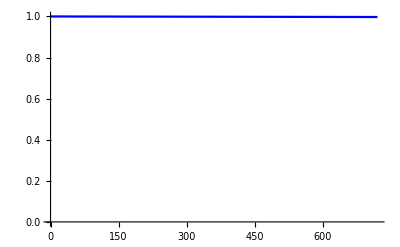

```mathematica
plot1m=ListLinePlot[prob1movr2y, PlotStyle->Blue, PlotRange->{0,1}]
```

```mathematica
probnoreinf3mtimecourse=Take[sarscov2probnoreinfectiontimecourse,90];
probnoreinf3m=Part[sarscov2probnoreinfectiontimecourse, 90];
prob3movr6y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,23]];
prob3movr2y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,7]];
```

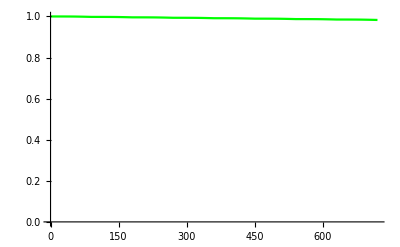

```mathematica
plot3m=ListLinePlot[prob3movr2y, PlotStyle->Green, PlotRange->{0,1}]
```

```mathematica
probnoreinf6mtimecourse=Take[sarscov2probnoreinfectiontimecourse,183];
probnoreinf6m=Part[sarscov2probnoreinfectiontimecourse, 183];
prob6movr6y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,11]];
prob6movr2y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,3]];
```

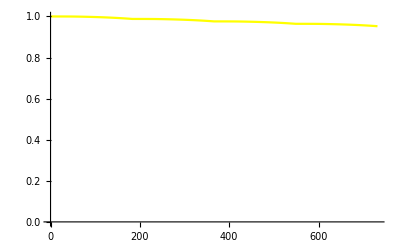

```mathematica
plot6m=ListLinePlot[prob6movr2y, PlotStyle->Yellow, PlotRange->{0,1}]
```

```mathematica
probnoreinf1ytimecourse=Take[sarscov2probnoreinfectiontimecourse,365];
probnoreinf1y=Part[sarscov2probnoreinfectiontimecourse, 365];
prob1yovr6y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,5]];
prob1yovr2y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,1]];
```

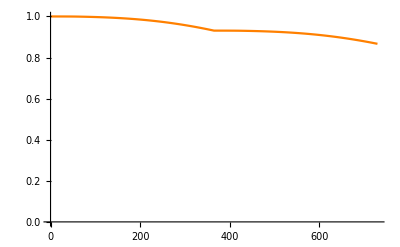

```mathematica
plot1y=ListLinePlot[prob1yovr2y, PlotStyle->Orange, PlotRange->{0,1}]
```

```mathematica
probnoreinf2ytimecourse=Take[sarscov2probnoreinfectiontimecourse,730];
probnoreinf2y=Part[sarscov2probnoreinfectiontimecourse, 730];
prob2yovr6y=Catenate[NestList[#*probnoreinf2y&,probnoreinf2ytimecourse,2]];
prob2yovr2y=Take[sarscov2probnoreinfectiontimecourse,730];
```

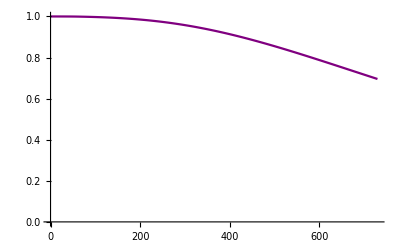

```mathematica
plot2y=ListLinePlot[prob2yovr2y, PlotStyle->Purple, PlotRange->{0,1}]
```

```mathematica
probnoreinf6ytimecourse=Take[sarscov2probnoreinfectiontimecourse,2190];
```

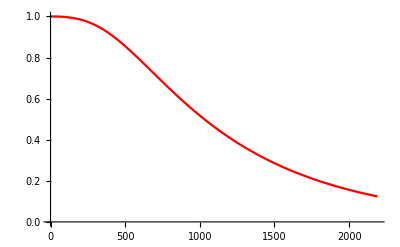

```mathematica
plot6y=ListLinePlot[probnoreinf6ytimecourse, PlotStyle->Red, PlotRange->{0,1}]
```

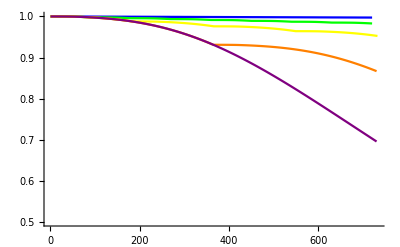

```mathematica
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1}]
```

```mathematica
Export[
StringJoin["/Users/hayley/Documents/townsend/spring-23/cancer/figs/hsct_boosterovrtime-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

/Users/hayley/Documents/townsend/spring-23/cancer/figs/hsct_boosterovrtime-by-Day_04May2023.pdf

```mathematica
Show[1-Last[prob2yovr2y], 1-Last[prob1yovr2y], 1-Last[prob6movr2y], 1-Last[prob3movr2y],1-Last[prob1movr2y]]
```

Show::gcomb: Could not combine the graphics objects in Show[0.304348,0.133148,0.0474436,0.0170445,0.0026989].

Show[0.304348,0.133148,0.0474436,0.0170445,0.0026989]

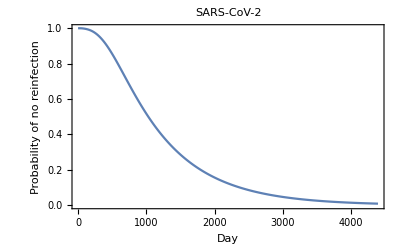

```mathematica
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
Export[
StringJoin["/Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_04May2023.pdf.

$Failed

```mathematica
sarscov2continuousprobnoreinfection=Interpolation[sarscov2probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{320.931,10.6977,0.879264}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1029.81,34.327,2.8214}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{2940.89,98.0298,8.05724}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov2probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov2probreinfectiondensity, 
If[day<1201,
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day]]]*sarscov2probnoreinfectiontimecourse[[day]],
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]]*sarscov2probnoreinfectiontimecourse[[day]]
]
]
];
```

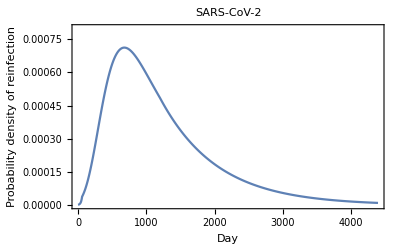

```mathematica
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0008},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0005},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_04May2023.pdf.

$Failed